# Artillery Aim Simulator

## Collin Davis and Chandler Jensen

## General Information:

I believe the easiest way to go about this project is to pick an artillery weapon currently in use by the United States military and use it for our simulation. Perhaps if we were to continue the project beyond the class we could add different weapons and allow the user to pick, but let’s not get ahead of ourselves.

Wikipedia has some good info on different artillery weapons, I think the M777 Howitzer is a good choice, coupled with the 155mm M795 shell. It has the following specifications (according to Wikipedia):
Range of Elevation: 0° - +71.7°
Muzzle Velocity: 827 m/s
Effective Firing Range: 22.5km

## Global Variables:

```mathematica
V0=827; (* V0 is the initial velocity of the shell *)
maxRange=22500; (* maximum range of the cannon *)
elevationMin=0Degree; (* minimum angle between horizontal plane and cannon *)
elevationMax=71.7Degree; (* maximum angle between horizontal plane and cannon *)
ShellWeight=46.7;(*this is the weight of the shell in kg*)
```

## Random Conditions Generator:

### Execute the Following Cell to Generate Random Conditions

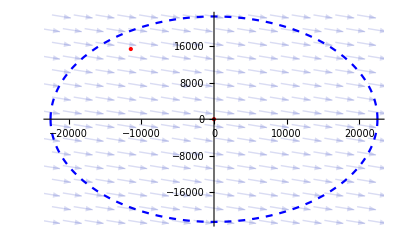

Target Position is:

{-11448.2,15365.2}

Wind Speed is:

11.2439 m/s

```mathematica
(* Wind Generation *)
windSpeed=RandomReal[{0,20}];
(* I chose 20 m/s as the maximum windspeed as the Beaufort wind scale classifies this windspeed as "Gale" *)
windDirection=RandomReal[{0,2π}];
windVector=AngleVector[{windSpeed,windDirection}];
windPlot=VectorPlot[windVector,{x,-maxRange,maxRange},{y,-maxRange,maxRange},VectorStyle->Opacity[0.15]];

(* Target Location Generation *)
rangePlot=Plot[{y=Sqrt[maxRange^2-x^2],y=-Sqrt[maxRange^2-x^2]},{x,-maxRange,maxRange},PlotRange->All,PlotStyle->{{Blue,Dashed},{Blue,Dashed}}];
targetPosition={RandomReal[{-maxRange,maxRange}],RandomReal[{-maxRange,maxRange}]} ;
While[targetPosition[[1]]^2+targetPosition[[2]]^2>maxRange^2,targetPosition={RandomReal[{-maxRange,maxRange}],RandomReal[{-maxRange,maxRange}]}]
targetX=targetPosition[[1]];
targetY=targetPosition[[2]];
artilleryPosition={0,0};
positionPlot=ListPlot[{targetPosition,artilleryPosition},AxesOrigin->{0,0},PlotRange->{{-maxRange,maxRange},{-maxRange,maxRange}},PlotStyle->{Red,PointSize[Large]}];

(* Random Conditions Plot *)
Show[positionPlot,windPlot,rangePlot]
"Target Position is:"
targetPosition
"Wind Speed is:"
windSpeed "m/s"
```

## Aiming The Weapon:

```mathematica
AutoAim[xposition_,yposition_,zposition_]:= Module[{x=xposition,y=yposition,z=zposition},direction=ArcTan[y/x];](*this is the direction and angle if there is no air resistance or wind*)
```